```mathematica
cphase={{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,-1}};
```

```mathematica
H={{1,1},{1,-1}}/Sqrt[2];
```

```mathematica
S={{1,0},{0,I}};
```

```mathematica
HH=KroneckerProduct[H,H];
```

```mathematica
HS=KroneckerProduct[H,S];
```

```mathematica
SH=KroneckerProduct[S,H];
```

```mathematica
SS=KroneckerProduct[S,S];
```

```mathematica
HI=KroneckerProduct[H,IdentityMatrix[2]];
```

```mathematica
SI=KroneckerProduct[S,IdentityMatrix[2]];
```

```mathematica
IH=KroneckerProduct[IdentityMatrix[2],H];
```

```mathematica
IS=KroneckerProduct[IdentityMatrix[2],S];
```

```mathematica
scaledQ[m1_,m2_]:=MatrixRank[{Flatten@m1,Flatten@m2}]==1
```

```mathematica
phases=Table[Exp[n Pi I /4],{n,0,7}];
```

```mathematica
phaseQ[m1_, m2_]:=Assuming[c∈phases,Reduce[m1==c m2]=!=False]
```

```mathematica
getNewMatrices[matrices_]:=Module[{newMatrices,newWords,keepList,keptMatrices,keptWords},
newMatrices=Flatten[Outer[Dot,matrixGenSet,matrices[[1]],1],1];
newWords=Flatten[Outer[StringJoin,wordGenSet,matrices[[2]],1],1];
keepList=(!AnyTrue[matrices[[1]],Function[M,scaledQ[#,M]],1])&/@newMatrices;
keptMatrices=Pick[newMatrices,keepList];
keptWords=Pick[newWords,keepList];
{keptMatrices,keptWords}=If[Length[keptMatrices]>1,Transpose[Union[Transpose[{keptMatrices,keptWords}],SameTest->Function[{x,y},scaledQ[First[x],First[y]]]]],{keptMatrices,keptWords}];
Return[{Join[keptMatrices,matrices[[1]]],Join[keptWords,matrices[[2]]]}]]
```

## Generate C2 using the shortest words

```mathematica
count=0;(matrices=NestWhile[(Print[count++];
Union[#~Join~Flatten[Outer[Dot,{HH,HS,SH,SS,cphase},#,1],1]])&,{IdentityMatrix[4]},Length[#2]≠Length[#1]&,2,99])//Length//Timing
```

0

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

{190.234,92160}

```mathematica
count=0;(C1matrices=NestWhile[(Print[count++];
Union[#,Flatten[Outer[Dot,{H,S},#,1],1],SameTest->scaledQ])&,{IdentityMatrix[2]},Length[#2]≠Length[#1]&,2,99])//Length//Timing
```

0

1

2

3

4

5

6

{0.140625,24}

```mathematica
matrixGenSet={H,S};
```

```mathematica
wordGenSet={"0","1"};
```

```mathematica
count=0;(C1matrices=NestWhile[(Print[count++];
getNewMatrices[#])&,{matrixGenSet,wordGenSet},Length[#[[1]]]≠24&,2,99]);
```

0

1

2

3

4

5

```mathematica
matrixGenSet={cphase,HI,SI,IH,IS};
```

```mathematica
wordGenSet={"0","1","2","3","4"};
```

```mathematica
count=0;(C2matrices=NestWhile[(Print[count++];
getNewMatrices[#])&,{matrixGenSet,wordGenSet},Length[#[[1]]]≠11520&,2,99]);
```

0

1

2

3

4

5

6

7

8

9

10

11

12

13

```mathematica
(*Export["C2matrices_no_phase_duplicates.mx",C2matrices]
```

C2matrices_no_phase_duplicates.mx

```mathematica
(*Export["C2matrices",C2matrices,"Table"]
```

C2matrices

```mathematica
(*Export["C2matrices_shortest_words",C2matrices[[2]],"Table"]
```

C2matrices_shortest_words

```mathematica
numZeros=StringCount[C2matrices[[2]],"0"];
```

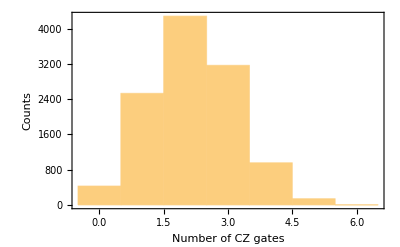

```mathematica
Histogram[numZeros,FrameLabel->{"Number of CZ gates","Counts"},Frame->{True,True,False,False}]
```

```mathematica
N[Mean[numZeros]]
```

2.18533

```mathematica
wordLengths=StringLength@C2matrices[[2]];
```

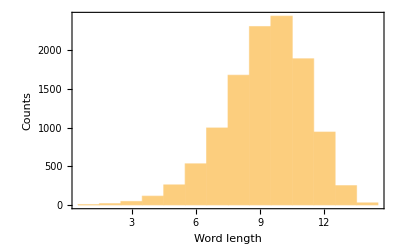

```mathematica
Histogram[wordLengths,FrameLabel->{"Word length","Counts"},Frame->{True,True,False,False}]
```

## Generate C2 using the fewest CZs

```mathematica
getNewMatricesNoPhaseTest[matrices_]:=Module[{newMatrices,newWords,TotalMatrices,TotalWords,uniqueMatrices},
newMatrices=Flatten[Outer[Dot,matrixGenSet,matrices[[1]],1],1];
newWords=Flatten[Outer[StringJoin,wordGenSet,matrices[[2]],1],1];
TotalMatrices=Join[newMatrices,matrices[[1]]];
TotalWords=Join[newWords,matrices[[2]]];
uniqueMatrices=Union[newMatrices,matrices[[3]]];
Return[{TotalMatrices,TotalWords,uniqueMatrices}]]
```

```mathematica
matrixGenSet={H,S};
```

```mathematica
wordGenSet={"0","1"};
```

```mathematica
temp=Flatten[Outer[Dot,matrixGenSet,matrixGenSet,1],1];
```

```mathematica
tempWords=Flatten[Outer[StringJoin,wordGenSet,wordGenSet,1],1];
```

```mathematica
temp2=DeleteDuplicates[Join[temp,matrixGenSet]];
```

```mathematica
temp3=MemberQ[temp2,#,1]&/@temp;
```

```mathematica
temp4=Join[Pick[tempWords,temp3],wordGenSet];
```

```mathematica
temp4
```

{00,01,10,11,0,1}

```mathematica
Nest[getNewMatricesNoPhaseTest,{matrixGenSet,wordGenSet,matrixGenSet},1]
```

{{{{1,0},{0,1}},{{1/(√2),ⅈ/(√2)},{1/(√2),-ⅈ/(√2)}},{{1/(√2),1/(√2)},{ⅈ/(√2),-ⅈ/(√2)}},{{1,0},{0,-1}},{{1/(√2),1/(√2)},{1/(√2),-1/(√2)}},{{1,0},{0,ⅈ}}},{00,01,10,11,0,1},{{{1,0},{0,-1}},{{1,0},{0,ⅈ}},{{1,0},{0,1}},{{1/(√2),ⅈ/(√2)},{1/(√2),-ⅈ/(√2)}},{{1/(√2),1/(√2)},{ⅈ/(√2),-ⅈ/(√2)}},{{1/(√2),1/(√2)},{1/(√2),-1/(√2)}}}}

```mathematica
count=0;(C1matrices=NestWhile[(Print["Count=",count++];
getNewMatricesNoPhaseTest[#])&,{matrixGenSet,wordGenSet},Length[#[[3]]]≠192&,2,99]);
```

Count=0

Part::partw: Part 3 of {{{{1/(√2),1/(√2)},{1/(√2),-1/(√2)}},{{1,0},{0,ⅈ}}},{0,1}} does not exist.

Union::heads: Heads Part and List at positions 2 and 1 are expected to be the same.

Part::partw: Part 3 of {{{{1/(√2),1/(√2)},{1/(√2),-1/(√2)}},{{1,0},{0,ⅈ}}},{0,1}} does not exist.

Count=1

Union::heads: Heads Part and List at positions 3 and 1 are expected to be the same.

Count=2

Union::heads: Heads Part and List at positions 4 and 1 are expected to be the same.

General::stop: Further output of Union::heads will be suppressed during this calculation.

Count=3

Count=4

Count=5

Count=6

Count=7

Count=8

Count=9

Count=10

Count=11

Count=12

$Aborted